```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ρ1[x_,rx_,ry_,n_]:=ry (1-Abs[x/rx]^n)^(1/n)
ρ2[x_,rx_,ry_,n_]:=-ry (1-Abs[x/rx]^n)^(1/n)
```

```mathematica
Export["LameEllipse.eps",
Plot[{ρ1[x,3,1,0.5],ρ1[x,3,1,1],ρ1[x,3,1,2],ρ1[x,3,1,5],ρ2[x,3,1,0.5],ρ2[x,3,1,1],ρ2[x,3,1,2],ρ2[x,3,1,5]},{x,-3,3},PlotRange->All,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","x_2"},PlotStyle->{Black,{Black,Dashing[0.025]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->{"n = 0.5", "n = 1", "n = 2", "n = 5"}]
]
```

LameEllipse.eps

```mathematica
ρ[x_,y_,rx_,ry_,n_]:=(Abs[x/rx]^n+Abs[y/ry]^n)^(1/n)
ϕ[x_,y_,p_,q_,rx_,ry_,n_]:=Piecewise[{{(p n)/(4rx ry Beta[1/n,1/n] Beta[2/p,q+1])(1-(Abs[x/rx]^n+Abs[y/ry]^n)^(p/n))^q, Abs[x/rx]^n+Abs[y/ry]^n≤1}, {0, Abs[x/rx]^n+Abs[y/ry]^n>1}}]
```

```mathematica
N0=10;
Msh={Table[Line[{{0,n/N0},{1,n/N0}}],{n,0,N0}],Table[Line[{{n/N0,0},{n/N0,1}}],{n,0,N0}]};
points=Table[{Point[{{0.025+n/N0,0.025+m/N0},{0.025+n/N0,0.075+m/N0},{0.075+n/N0,0.025+m/N0},{0.075+n/N0,0.075+m/N0}}]},{n,0,N0-1},{m,0,N0-1}];
circ=Circle[{0.075+4/N0,0.075+7/N0},0.21];
cros={Line[{{0.075+4/N0-0.01,0.075+7/N0-0.01},{0.075+4/N0+0.01,0.075+7/N0+0.01}}],Line[{{0.075+4/N0-0.01,0.075+7/N0+0.01},{0.075+4/N0+0.01,0.075+7/N0-0.01}}]};
approx={Rectangle[{0.3,0.6},{0.7,0.9}],Rectangle[{0.3,0.9},{0.6,1}],Rectangle[{0.2,0.7},{0.3,0.9}],Rectangle[{0.4,0.5},{0.6,0.6}]};
(*Export["ApproxSQ.eps",*)
Graphics[{Thick,Msh,points,cros,Opacity[0.2],approx,Opacity[1],Thickness[0.006], circ},ImageSize->Large]
```

ApproxSQ.eps

```mathematica
N0=10;
Msh={Table[Line[{{0,n/N0},{1,n/N0}}],{n,0,N0}],Table[Line[{{n/N0,0},{n/N0,1}}],{n,0,N0}]};
points=Table[Point[{0.05+n/N0,0.05+m/N0}],{n,0,N0-1},{m,0,N0-1}];
circ=Circle[{0.05+4/N0,0.05+7/N0},0.21];
cros={Line[{{0.05+4/N0-0.01,0.05+7/N0-0.01},{0.05+4/N0+0.01,0.05+7/N0+0.01}}],Line[{{0.05+4/N0-0.01,0.05+7/N0+0.01},{0.05+4/N0+0.01,0.05+7/N0-0.01}}]};
approx={Rectangle[{0.3,0.6},{0.6,0.9}],Rectangle[{0.2,0.7},{0.3,0.8}],Rectangle[{0.6,0.7},{0.7,0.8}],Rectangle[{0.4,0.5},{0.5,0.6}],Rectangle[{0.4,0.9},{0.5,1.0}]};
Export["ApproxS.eps",
Graphics[{Thick,Msh,points,cros,Opacity[0.2],approx,Opacity[1],Thickness[0.006], circ},ImageSize->Large]
]
```

ApproxS.eps

```mathematica
Export["OpenMPAcceleration.eps",
BarChart[{{
Labeled[3.4,Rotate["2500",π/2],Bottom],
Labeled[4.5,Rotate["10000",π/2],Bottom],
Labeled[5.4,Rotate["40000",π/2],Bottom],
Labeled[11.2,Rotate["2500, r = 0.05",π/2],Bottom],
Labeled[12.9,Rotate["10000, r = 0.05",π/2],Bottom],
Labeled[13.5,Rotate["40000, r = 0.05",π/2],Bottom],
Labeled[13.4,Rotate["2500, r = 0.1",π/2],Bottom],
Labeled[13.9,Rotate["10000, r = 0.1",π/2],Bottom],
Labeled[14.2,Rotate["40000, r = 0.1",π/2],Bottom]
}},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"","t_1/t_16"},LabelingFunction->Above,ChartStyle->Directive[EdgeForm[{Thick,Black}], White]]
]
```

OpenMPAcceleration.eps

```mathematica
Export["MPIAcceleration.eps",
BarChart[{{
Labeled[3.3,Rotate["10000, r = 0.05, mem",π/2],Bottom],
Labeled[3.1,Rotate["10000, r = 0.1, mem",π/2],Bottom],
Labeled[3.1,Rotate["40000, r = 0.05, mem",π/2],Bottom],
Labeled[3.1,Rotate["40000, r = 0.1, mem",π/2],Bottom],
Labeled[3.9,Rotate["10000, r = 0.05, speed",π/2],Bottom],
Labeled[3.8,Rotate["40000, r = 0.05, speed",π/2],Bottom],
Labeled[3.6,Rotate["10000, r = 0.1, speed",π/2],Bottom],
Labeled[3.7,Rotate["40000, r = 0.1, speed",π/2],Bottom]
}},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"","t_16/max_p t_16^p"},LabelingFunction->Above,ChartStyle->Directive[EdgeForm[{Thick,Black}], White]]
]
```

MPIAcceleration.eps

```mathematica
(*Time speed balancing*)
Export["TimeSpeedBalancing.eps",
PieChart[{55.41,54.8,57.47,59.91},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"t_16^1 = 55 s","t_16^2 = 54 s","t_16^3 = 57 s","t_16^4 = 60 s"}]
]
```

TimeSpeedBalancing.eps

```mathematica
(*Memory speed balancing*)
Export["MemorySpeedBalancing.eps",
PieChart[{1.9,1.9,1.9,4.5},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"V_1 = 1.9 Gb","V_2 = 1.9 Gb","V_3 = 1.9 Gb","V_4 = 4.5 Gb"}]
]
```

MemorySpeedBalancing.eps

```mathematica
(*Time memory balancing*)
Export["TimeMemoryBalancing.eps",
PieChart[{72.66,72.46,45.91,34.72},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"t_16^1 = 72 s","t_16^2 = 72 s","t_16^3 = 46 s","t_16^4 = 35 s"}]
]
```

TimeMemoryBalancing.eps

```mathematica
(*Memory memory balancing*)
Export["MemoryMemoryBalancing.eps",
PieChart[{2.5,2.6,2.5,2.6},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],ChartStyle->Directive[EdgeForm[{Thick,Black}], White],ChartLabels->{"V_1 = 2.5 Gb","V_2 = 2.6 Gb","V_3 = 2.5 Gb","V_4 = 2.6 Gb"}]
]
```

MemoryMemoryBalancing.eps

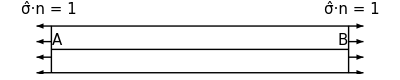

```mathematica
rect=Line[{{0,0},{10,0},{10,1},{0,1},{0,0}}];
M0=3;
FZ=15;
LeftP=Table[Arrow[{{0,n/M0},{-0.5,n/M0}}],{n,0,M0}];
RightP=Table[Arrow[{{10,n/M0},{10.5,n/M0}}],{n,0,M0}];
σnL=Text[Style["σ̂·n = 1",FZ],{-0.1,1.35}];
σnR=Text[Style["σ̂·n = 1",FZ],{10.1,1.35}];
AB={Line[{{0,0.5},{10,0.5}}],Text[Style["A",FZ],{0.2,0.7}],Text[Style["B",FZ],{9.8,0.7}]};
(*Export["LongRect.eps",*)
Graphics[{Thick,Arrowheads[0.02],rect,LeftP,RightP,σnL,σnR,AB},ImageSize->Full]
```

```mathematica
Export["AppLoadF.eps",
Plot[{1,Piecewise[{{4x, x≤0.5}, {4-4x, x>0.5}}],Piecewise[{{2-4x, x≤0.5}, {4x-2, x>0}}]},{x,0,1},ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x","f"},PlotStyle->{Black,{Black,Dashing[0.025]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->{"f = f_1", "f = f_2", "f = f_3"}]
]
```

AppLoadF.eps

```mathematica
σ11Uniform=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/sigma11.csv"]];
σ11Triangle=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_triangle/sigma11.csv"]];
σ11InvTriangle=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_inv_triangle/sigma11.csv"]];
σ11ShortUniform=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_short_uniform/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
y0=0.;
Export["LongRectStress11VarFx200.eps",
Show[
Plot[{σ11Uniform[x,y0],σ11Triangle[x,y0],σ11InvTriangle[x,y0]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","(σ̄)_11"},PlotStyle->{Black,{Black,Dashing[0.05]},{Black,DotDashed},{Black,Dashing[0.05]}},PlotLegends->Placed[{"f_1","f_2","f_3","f_4"},Scaled[{0.7,0.8}]]],
Graphics[{Text[Style["r = 0.2",22],Scaled[{0.35,0.95}]],Text[Style["x_2 = 0",22],Scaled[{0.35,0.85}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.75}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.65}]]}]
]
]
```

LongRectStress11VarFx200.eps

```mathematica
σ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma11.csv"]];
σ11p12r005=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r005/sigma11.csv"]];
σ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma11.csv"]];
σ11p12r02=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectStress11VarR.eps",
Show[
Plot[{σ11Loc[5,y],σ11p12r005[5,y],σ11p12r01[5,y],σ11p12r02[5,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.35}]]}]
]
]
```

LongRectStress11VarR.eps

```mathematica
σ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma11.csv"]];
σ11p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/sigma11.csv"]];
σ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma11.csv"]];
σ11p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/sigma11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectStress11VarP.eps",
Show[
Plot[{σ11Loc[5,y],σ11p23r01[5,y],σ11p12r01[5,y],σ11p13r01[5,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 1","p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.35}]]}]
]
]
```

LongRectStress11VarP.eps

```mathematica
σ12Loc=Interpolation[Import["data/LongRect/LongRect_loc/sigma12.csv"]];
σ12p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/sigma12.csv"]];
σ12p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/sigma12.csv"]];
σ12p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/sigma12.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

```mathematica
Export["LongRectSigma12X1.eps",
Show[
Plot[{σ12p23r01[x,0.1],σ12p12r01[x,0.1],σ12p13r01[x,0.1]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","(σ̄)_12"},PlotStyle->{{Black,DotDashed},Black,{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.78}]]],
Graphics[{Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.96}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.84}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.72}]],Text[Style["f = f_1",22],Scaled[{0.35,0.6}]]}]
]
]
```

LongRectSigma12X1.eps

```mathematica
Export["LongRectSigma12X2.eps",
Show[
Plot[{σ12Loc[0.1,y],σ12p23r01[0.1,y],σ12p12r01[0.1,y],σ12p13r01[0.1,y]},{y,0,1},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"p_1 = 2/3","p_1 = 1/2","p_1 = 1/3"},Scaled[{0.7,0.8}]]],
Graphics[{Text[Style["x_2 = 0.1",22],Scaled[{0.35,0.95}]],Text[Style["r = 0.1",22],Scaled[{0.35,0.8}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.65}]]}]
]
]
```

LongRectSigma12X2.eps

```mathematica
ϵ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/eps11.csv"]];
ϵ11p12r005=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r005/eps11.csv"]];
ϵ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/eps11.csv"]];
ϵ11p12r02=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02/eps11.csv"]];
```

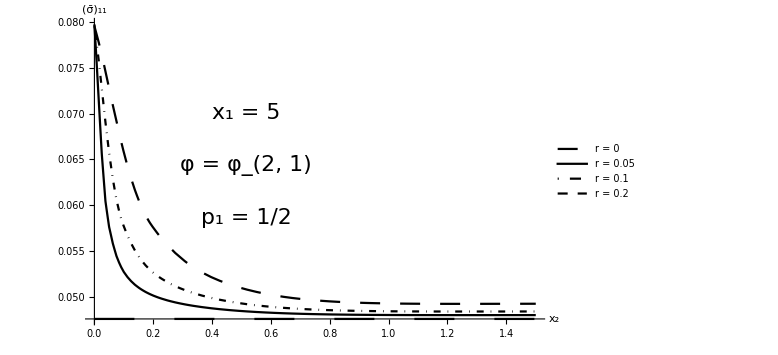

```mathematica
y0=0.;
Show[
Plot[{ϵ11Loc[x,y0],ϵ11p12r005[x,y0],ϵ11p12r01[x,y0],ϵ11p12r02[x,y0]},{x,0,1.5},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.35}]]}]
]
```

```mathematica
ϵ11Loc=Interpolation[Import["data/LongRect/LongRect_loc/eps11.csv"]];
ϵ11p23r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p23_r01/eps11.csv"]];
ϵ11p12r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r01/eps11.csv"]];
ϵ11p13r01=Interpolation[Import["data/LongRect/LongRect_nonloc_p13_r01/eps11.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

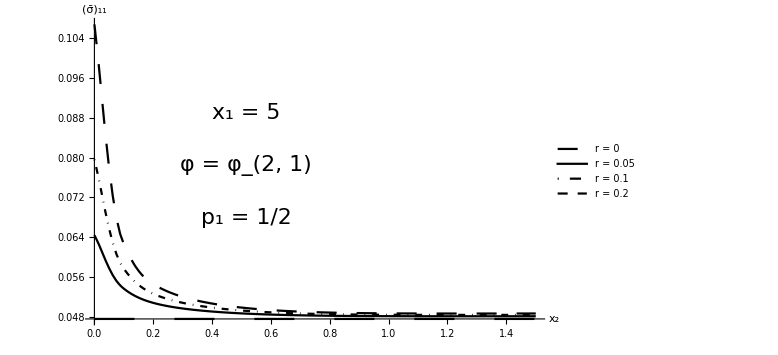

```mathematica
y0=0.;
Show[
Plot[{ϵ11Loc[x,y0],ϵ11p23r01[x,y0],ϵ11p12r01[x,y0],ϵ11p13r01[x,y0]},{x,0,1.5},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_2","(σ̄)_11"},PlotStyle->{{Black,Dashing[0.05]},Black,{Black,DotDashed},{Black,Dashing[0.025]}},PlotLegends->Placed[{"r = 0","r = 0.05","r = 0.1","r = 0.2"},Scaled[{0.7,0.5}]]],
Graphics[{Text[Style["x_1 = 5",22],Scaled[{0.35,0.69}]],Text[Style["φ = φ_(2, 1)",22],Scaled[{0.35,0.52}]],Text[Style["p_1 = 1/2",22],Scaled[{0.35,0.35}]]}]
]
```

```mathematica
u1Loc=Interpolation[Import["data/LongRect/LongRect_loc/u1.csv"]];
u1NonLocP1Q1=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p1_q1/u1.csv"]];
u1NonLocP3Q1=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p3_q1/u1.csv"]];
u1NonLocP5Q1=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p5_q1/u1.csv"]];
u1NonLocConst=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_const/u1.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

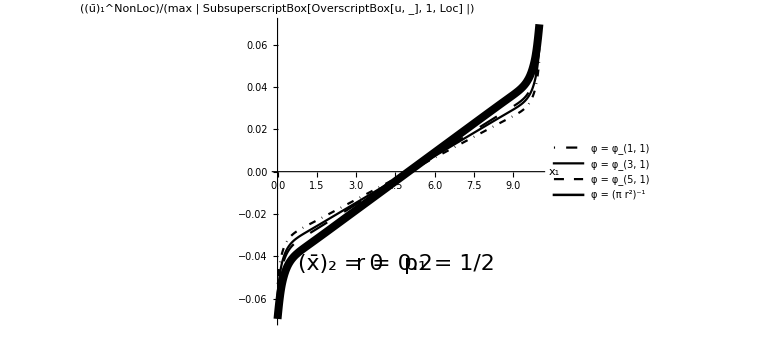

```mathematica
y0=0.0;
Show[
Plot[{(u1NonLocP1Q1[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocP3Q1[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocP5Q1[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocConst[x,y0]-u1Loc[x,y0])/u1Loc[10,0]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","((ū)_1^NonLoc)/(max | SubsuperscriptBox[OverscriptBox[u, _], 1, Loc] |)"},PlotStyle->{{Black,DotDashed},Black,{Black,Dashing[0.025]},{Black,Thickness[0.01]}}(*,PlotLegends->Placed[{"φ = φ_(1, 1)","φ = φ_(3, 1)","φ = φ_(5, 1)","φ = (π r^2)^-1"},Scaled[{0.25,0.75}]]*)],
Plot[{-100,-200},{x,0,10},LabelStyle->Directive[{Black,FontSize->22}],PlotStyle->{{Black,DotDashed},Black},
PlotLegends->Placed[{"φ = φ_(1, 1)","φ = φ_(3, 1)"},Scaled[{0.25,0.8}]]],
Plot[{-100,-200},{x,0,10},LabelStyle->Directive[{Black,FontSize->22}],PlotStyle->{{Black,Dashing[0.025]},{Black,Thickness[0.01]}},
PlotLegends->Placed[{"φ = φ_(5, 1)","φ = (π r^2)^-1"},Scaled[{0.6,0.8}]]],
Graphics[{Text[Style["(x̄)_2 = 0",22],Scaled[{0.25,0.2}]],Text[Style["r = 0.2",22],Scaled[{0.45,0.2}]],Text[Style["p_1 = 1/2",22],Scaled[{0.65,0.2}]]}]
]
```

```mathematica
u1Loc=Interpolation[Import["data/LongRect/LongRect_loc/u1.csv"]];
u1NonLocP1Q1=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p1_q1/u1.csv"]];
u1NonLocP1Q2=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p1_q2/u1.csv"]];
u1NonLocP1Q3=Interpolation[Import["data/LongRect/LongRect_nonloc_p12_r02_p1_q3/u1.csv"]];
```

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

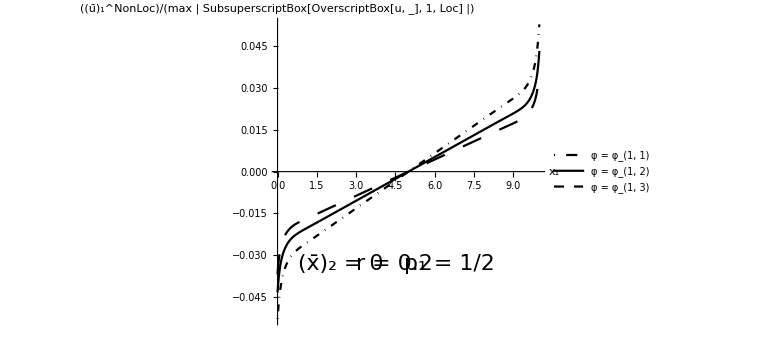

```mathematica
Show[
Plot[{(u1NonLocP1Q1[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocP1Q2[x,y0]-u1Loc[x,y0])/u1Loc[10,0],(u1NonLocP1Q3[x,y0]-u1Loc[x,y0])/u1Loc[10,0]},{x,0,10},PlotRange->Full,ImageSize->Large,LabelStyle->Directive[{Black,FontSize->22}],AxesLabel->{"x_1","((ū)_1^NonLoc)/(max | SubsuperscriptBox[OverscriptBox[u, _], 1, Loc] |)"},PlotStyle->{{Black,DotDashed},Black,{Black,Dashing[0.025]},{Black,Thickness[0.01]}},PlotLegends->Placed[{"φ = φ_(1, 1)","φ = φ_(1, 2)","φ = φ_(1, 3)"},Scaled[{0.4,0.8}]]],
Graphics[{Text[Style["(x̄)_2 = 0",22],Scaled[{0.25,0.2}]],Text[Style["r = 0.2",22],Scaled[{0.45,0.2}]],Text[Style["p_1 = 1/2",22],Scaled[{0.65,0.2}]]}]
]
```